# 1D Discrete Quantum Mechanics

Paul Schulz <paul@mawsonlakes.org>

## Motivation

Feynman Nobel Prize Lecture  - https://www.nobelprize.org/prizes/physics/1965/feynman/lecture/

...
Another problem on which I struggled very hard, was to represent relativistic electrons with this new quantum mechanics. I wanted to do a unique and different way – and not just by copying the operators of Dirac into some kind of an expression and using some kind of Dirac algebra instead of ordinary complex numbers. I was very much encouraged by the fact that in one space dimension, I did find a way of giving an amplitude to every path by limiting myself to paths, which only went back and forth at the speed of light. The amplitude was simple (ie) to a power equal to the number of velocity reversals where I have divided the time into steps and I am allowed to reverse velocity only at such a time. This gives (as approaches zero) Dirac’s equation in two dimensions – one dimension of space and one of time￼.

Dirac’s wave function has four components in four dimensions, but in this case, it has only two components and this rule for the amplitude of a path automatically generates the need for two components. Because if this is the formula for the amplitudes of path, it will not do you any good to know the total amplitude of all paths, which come into a given point to find the amplitude to reach the next point. This is because for the next time, if it came in from the right, there is no new factor ie if it goes out to the right, whereas, if it came in from the left there was a new factor ie. So, to continue this same information forward to the next moment, it was not sufficient information to know the total amplitude to arrive, but you had to know the amplitude to arrive from the right and the amplitude to arrive to the left, independently. If you did, however, you could then compute both of those again independently and thus you had to carry two amplitudes to form a differential equation (first order in time).

And, so I dreamed that if I were clever, I would find a formula for the amplitude of a path that was beautiful and simple for three dimensions of space and one of time, which would be equivalent to the Dirac equation, and for which the four components, matrices, and all those other mathematical funny things would come out as a simple consequence – I have never succeeded in that either. But, I did want to mention some of the unsuccessful things on which I spent almost as much effort, as on the things that did work.
...

## Preliminaries

```mathematica
PacletDataRebuild[]
```

```mathematica
initgraph1 = {{0,0},{0,0},{0,0}};
```

```mathematica
rule = {{0,0},{0,0}} -> {{0,0}};
```

```mathematica
ResourceFunction["WolframModelPlot"][initgraph1]
```

WolframModel::shdw: Symbol WolframModel appears in multiple contexts {SetReplace`,Global`}; definitions in context SetReplace` may shadow or be shadowed by other definitions.

-Graphics-

```mathematica
RulePlot[WolframModel[rule]]
```

-Graphics-

```mathematica
ResourceFunction["WolframModel"] [{{0,0}}->{},{{0,0},{0,0},{0,0}},1,"StatesPlotsList"]
```

{-Graphics-,-Graphics-}

## Introduction

This paper describes how to grow a 2D lattice to support a 1D model of Quantum Mechanics using the Wolfram Physics Model.

## Underlying Spacetime Manifold

```mathematica
-Graphics-;
```

Want to create the above hypergraph and investigate how Quantum Mechanics can work with such a graph.

### Grow space array

We want to start with a 'zig zag' array which can then be extended/grown to as a causal graph.

```mathematica
rule = {{x,a},{y,a},{y,y},{y,y}}->{{x,a},{y,a},{y,b},{z,b},{b,b},{y,y},{z,z},{z,z}};
```

```mathematica
RulePlot[WolframModel[rule],VertexLabels->Automatic]
```

-Graphics-

It would be interesting if initial graph could be set as  the three times self loop as it is particularly attractive (simple).

```mathematica
initgraph1 = {{0,0},{0,0},{0,0}};
```

```mathematica
ResourceFunction["WolframModelPlot"][initgraph1]
```

-Graphics-

```mathematica
initgraph ={{0,1},{2,1},{1,1},{2,2},{2,2}} ;
```

```mathematica
ResourceFunction["WolframModelPlot"][initgraph,VertexLabels->Automatic]
```

-Graphics-

```mathematica
ResourceFunction["WolframModel"] [rule,initgraph,5,"StatesPlotsList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ResourceFunction["WolframModel"] [rule,initgraph,10,"FinalStatePlot"]
```

-Graphics-

```mathematica
g=ResourceFunction["WolframModel"][rule,initgraph,10,"FinalState"];
```

```mathematica
WolframModelPlot[g,VertexLabels-> Automatic]
```

-Graphics-

### Add causal structure

Rewriting rules - Successful attempt number one. Need to use self loops as accounting trick to ensure rule is applied to the correct location only once.

```mathematica
rule2 = {{a,x},{b,x},{b,y},{c,y},{b,b}}-> {{a,x},{b,x},{b,y},{c,y},{x,i},{y,i},{i,i}};
```

```mathematica
RulePlot[WolframModel[rule2],VertexLabels->Automatic]
```

-Graphics-

```mathematica
WolframModel[rule2,g,10,"FinalStatePlot"]
```

-Graphics-

Rewriting rule attempt number 2. A simpler(shorter rule). Also removes double loop

```mathematica
rule3={{b,x},{b,y}, {b,b}}-> {{b,x},{b,y},{x,i},{y,i},{i,i}};
```

```mathematica
RulePlot[WolframModel[rule3],VertexLabels->Automatic]
```

-Graphics-

```mathematica
hg=WolframModel[rule3,g,15]
```

WolframModelEvolutionObject[…]

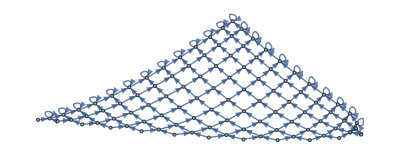

```mathematica
ResourceFunction["HypergraphToGraph"][WolframModel[rule3,g,15,"FinalState"]]
```

#### Properties

```mathematica
hg["VertexCountList"]
```

{23,34,45,55,64,72,79,85,90,94,97,99,100}

```mathematica
HypergraphNeighborhoodVolumeVolumes[hg]
```

HypergraphNeighborhoodVolumeVolumes[WolframModelEvolutionObject[…]]

```mathematica
hg["CausalGraph"]
```

-Graphics-

```mathematica
hg["LayeredCausalGraph"]
```

-Graphics-

#### Multiway System

```mathematica
WolframModel[rule3,g,15,"EventsStatesPlotsList"]
```

## Alternative

```mathematica
ruleA = {{2,1},{2,3},{3,3}} -> {{2,1},{2,3},{4,3},{4,5},{5,5}}
```

{{2,1},{2,3},{3,3}}→{{2,1},{2,3},{4,3},{4,5},{5,5}}

```mathematica
ruleB = {{2,1},{2,3}} -> {{1,2},{3,2}}
```

{{2,1},{2,3}}→{{1,2},{3,2}}

```mathematica
RulePlot[WolframModel[ruleA],VertexLabels->Automatic]
```

-Graphics-

```mathematica
initialState = {{2,1},{2,3},{3,3}}
```

{{2,1},{2,3},{3,3}}

```mathematica
gA = WolframModel[ruleA,initialState,10]
```

WolframModelEvolutionObject[…]

```mathematica
gA["FinalStatePlot"]
```

-Graphics-

```mathematica
gB = WolframModel[ruleB,gA["FinalState"],20]
```

WolframModelEvolutionObject[…]

```mathematica
gB["FinalStatePlot"]
```

-Graphics-

```mathematica
gB["LayeredCausalGraph"]
```

-Graphics-

```mathematica
gB["
```

See: https://www.wolframphysics.org/bulletins/2020/08/a-short-note-on-the-double-slit-experiment-and-other-quantum-interference-effects-in-the-wolfram-model/

```mathematica
WolframModelPlot[g,VertexLabels-> Automatic]
```

WolframModelPlot[g,VertexLabels→Automatic]